```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/Users/zack/Documents/oscillators/faraday

```mathematica
Needs["ErrorBarPlots`"]
directory="data"
filebase="flat2";
data0=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];filebase="periodic2";
data1=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];
filebase="random2";
data2=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

data

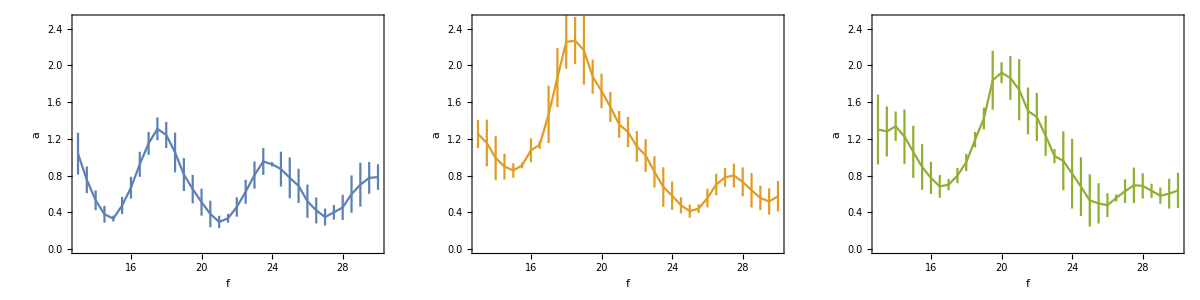

```mathematica
p0=ErrorListPlot[DeleteCases[#,{}]&/@{Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@Cases[data0,u_/;Abs[u[[3]]-freq]<0.25],{freq,13,30,0.5}]},Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotRange->{{13,30},{0,2.5}},Joined->True];
p1=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@Cases[data1,u_/;Abs[u[[3]]-freq]<0.25],{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[2]],PlotRange->{{13,30},{0,2.5}},Joined->True];
p2=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@Cases[data2,u_/;Abs[u[[3]]-freq]<0.25],{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[3]],PlotRange->{{13,30},{0,2.5}},Joined->True];
Grid[{{p0,p1,p2}}]
```

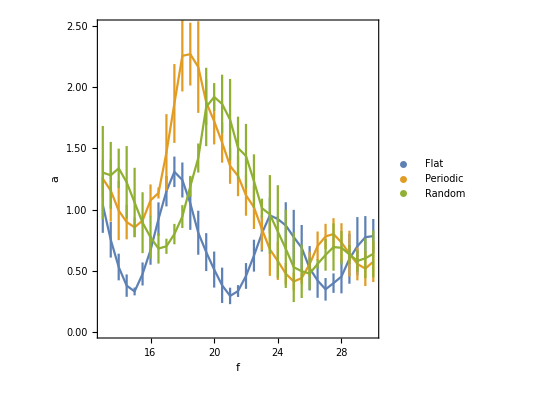

combined.pdf

```mathematica
p=Legended[Show[p0,p1,p2,FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,3.0,0.5}],Table[{i,""},{i,0,2.0,0.5}]},{Table[{i,i},{i,12,30,2}],Table[{i,""},{i,12,30,2}]}}],Placed[PointLegend[ColorData[97,"ColorList"][[1;;3]],{"Flat","Periodic","Random"},LabelStyle->Directive[16]],Right]]
Export["combined.pdf",p]
```

```mathematica
filebase="sweeps/flat2acc"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
p=rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["SouthwestColors"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,None}}],p0,PlotRange->{{13,30},{0,1.5}},ImageSize->300]]
Export["data/flatmodes.pdf",p]
```

sweeps/flat2acc

-Graphics-

data/flatmodes.pdf

```mathematica
filebase="sweeps/periodic2acc"
growth2=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
p=rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth2[[All,{1,2,5}]],Position[growth2[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["SouthwestColors"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,None}}],p1,PlotRange->{{13,30},{0,1.5}},ImageSize->300]]
```

sweeps/periodic2acc

-Graphics-

```mathematica
filebase="sweeps/random2acc"
growth3=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
p=rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth3[[All,{1,2,5}]],Position[growth3[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["SouthwestColors"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,None}}],p2,PlotRange->{{13,30},{0,1.5}},ImageSize->300]]
```

sweeps/random2acc

-Graphics-

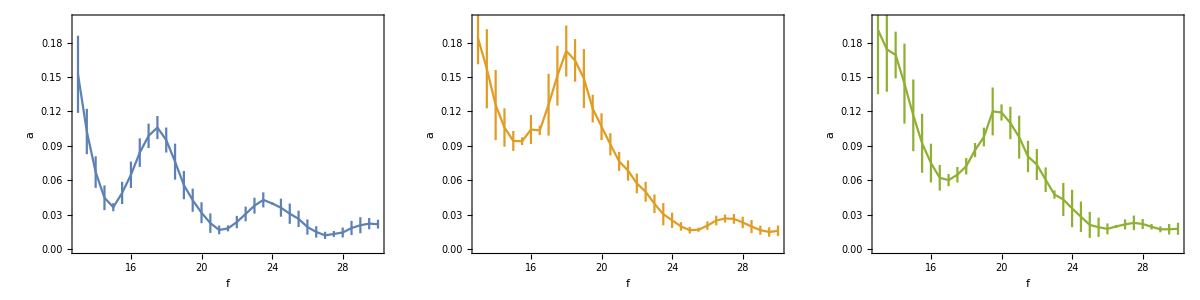

```mathematica
p0=ErrorListPlot[DeleteCases[#,{}]&/@{Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data0,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}]},Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotRange->{{13,30},{0,0.2}},Joined->True];
p1=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data1,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[2]],PlotRange->{{13,30},{0,0.2}},Joined->True];
p2=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data2,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[3]],PlotRange->{{13,30},{0,0.2}},Joined->True];
Grid[{{p0,p1,p2}}]
```

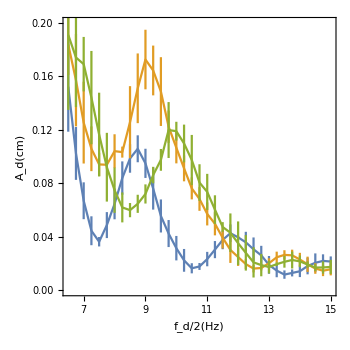

combined.pdf

```mathematica
p=Show[p0,p1,p2,FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.2,0.04}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i/2},{i,14,30,4}],Table[{i,""},{i,12,30,4}]}},FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},AspectRatio->1,ImageSize->350]
Export["combined.pdf",p]
```